## Benchmark 2: S-Shaped Nonuniform Growth -- A-SW on the Current

```mathematica
ClearAll["Global`*"];

(* ---------------------------------------------------------------- *)
(* 1. Three-dimensional kinematics and nonuniform growth            *)
(* ---------------------------------------------------------------- *)

κ[X_] := κ0 Sin[2 Pi X/L];
g[X_, Z_] := λG Exp[Z κ[X]];
G[X_, Z_] := {{g[X, Z], 0, 0}, {0, 1, 0}, {0, 0, 1}};

CheckGrowthExpansion = Normal[Series[g[X, Z], {Z, 0, 2}]] // FullSimplify

x[X_, Z_] := x0[X] + x1[X] Z + 1/2 x2[X] (Z^2 - h^2/3);
z[X_, Z_] := z0[X] + z1[X] Z + 1/2 z2[X] (Z^2 - h^2/3);
p[X_, Z_] := p0[X] + p1[X] Z;

F[X_, Z_] := {{D[x[X, Z], X], 0, D[x[X, Z], Z]}, {0, 1, 0}, {D[z[X, Z], X], 0, D[z[X, Z], Z]}};
A[X_, Z_] := F[X, Z] . Inverse[G[X, Z]];
```

λG+1/2 Z κ0 λG Sin[(2 π X)/L] (2+Z κ0 Sin[(2 π X)/L])

```mathematica
(* ---------------------------------------------------------------- *)
(* 2. Three-dimensional and reduced A-SW energy                     *)
(* ---------------------------------------------------------------- *)

JG[X_, Z_] := Det[G[X, Z]];
W[X_, Z_] := JG[X, Z] μ/2 (Tr[Transpose[A[X, Z]] . A[X, Z]] - 3);
R[X_, Z_] := JG[X, Z] (Det[A[X, Z]] - 1);
WAug[X_, Z_] := W[X, Z] - p[X, Z] R[X, Z];

qBar[X_] := {qBarx[X], qBarz[X]};
qHat[X_] := {qHatx[X], qHatz[X]};
qPlus[X_] := h qBar[X] + qHat[X];
qMinus[X_] := h qBar[X] - qHat[X];

u[X_, Z_] := {x[X, Z] - X, z[X, Z] - Z};

WAugZ2[X_] := Normal[Series[WAug[X, Z], {Z, 0, 2}]] // Expand // Simplify;

EaAswIntRaw[X_] := Integrate[WAugZ2[X], {Z, -h, h}];
EaAswLoadRaw[X_] := -(qPlus[X] . u[X, h] + qMinus[X] . u[X, -h]);

EaAswInt[X_] := Normal[Series[EaAswIntRaw[X], {h, 0, 3}]]/(2 h) // Expand // Simplify;
EaAswLoad[X_] := Normal[Series[EaAswLoadRaw[X], {h, 0, 3}]]/(2 h) // Expand // Simplify;

EaAsw[X_] := EaAswInt[X] + EaAswLoad[X] // Expand // Simplify;

EaAsw[X]
```

1/(12 λG)(-12 λG^2 μ+12 λG qHatz[X]+4 h^2 κ0 λG^2 p1[X] Sin[(2 π X)/L]-2 h^2 κ0^2 λG^2 μ Sin[(2 π X)/L]^2-12 λG qHatx[X] x1[X]+6 λG^2 μ x1[X]^2+h^2 κ0^2 λG^2 μ Sin[(2 π X)/L]^2 x1[X]^2+4 h^2 κ0 λG^2 μ Sin[(2 π X)/L] x1[X] x2[X]+2 h^2 λG^2 μ x2[X]^2+4 λG qBarx[X] (3 X-3 x0[X]-h^2 x2[X])-12 λG qBarz[X] z0[X]-12 λG qHatz[X] z1[X]+6 λG^2 μ z1[X]^2+h^2 κ0^2 λG^2 μ Sin[(2 π X)/L]^2 z1[X]^2-4 h^2 λG qBarz[X] z2[X]+4 h^2 κ0 λG^2 μ Sin[(2 π X)/L] z1[X] z2[X]+2 h^2 λG^2 μ z2[X]^2-4 h^2 λG p1[X] z2[X] x0'[X]+6 μ x0'[X]^2+h^2 κ0^2 μ Sin[(2 π X)/L]^2 x0'[X]^2-4 h^2 λG p1[X] z1[X] x1'[X]-4 h^2 κ0 μ Sin[(2 π X)/L] x0'[X] x1'[X]+2 h^2 μ x1'[X]^2+4 h^2 λG p1[X] x2[X] z0'[X]+6 μ z0'[X]^2+h^2 κ0^2 μ Sin[(2 π X)/L]^2 z0'[X]^2+4 h^2 λG p1[X] x1[X] z1'[X]-4 h^2 κ0 μ Sin[(2 π X)/L] z0'[X] z1'[X]+2 h^2 μ z1'[X]^2+2 λG p0[X] (6 λG+h^2 κ0^2 λG Sin[(2 π X)/L]^2-6 z1[X] x0'[X]-2 h^2 z2[X] x1'[X]+6 x1[X] z0'[X]+2 h^2 x2[X] z1'[X]))

```mathematica
(* ---------------------------------------------------------------- *)
(* 3. Step-wise stationarity equations                              *)
(* ---------------------------------------------------------------- *)

EqAswP0 = D[EaAsw[X], p0[X]] // FullSimplify;
EqAswP1 = D[EaAsw[X], p1[X]] // FullSimplify;

EqAsw11 = D[EaAsw[X], x1[X]] - D[D[EaAsw[X], x1'[X]], X] // FullSimplify;
EqAsw12 = D[EaAsw[X], z1[X]] - D[D[EaAsw[X], z1'[X]], X] // FullSimplify;

EqAsw21 = D[EaAsw[X], x2[X]] - D[D[EaAsw[X], x2'[X]], X] // FullSimplify;
EqAsw22 = D[EaAsw[X], z2[X]] - D[D[EaAsw[X], z2'[X]], X] // FullSimplify;

TruncH0[expr_] := Normal[Series[expr, {h, 0, 0}]] // Expand // FullSimplify;

EqAsw11L = TruncH0[EqAsw11];
EqAsw12L = TruncH0[EqAsw12];
EqAswP0L = TruncH0[EqAswP0];

EqAsw11L
EqAsw12L
EqAswP0L
EqAsw21
EqAsw22
EqAswP1
```

-qHatx[X]+λG μ x1[X]+p0[X] z0'[X]

-qHatz[X]+λG μ z1[X]-p0[X] x0'[X]

λG-z1[X] x0'[X]+x1[X] z0'[X]

1/3 h^2 (-qBarx[X]+λG μ (κ0 Sin[(2 π X)/L] x1[X]+x2[X])+p1[X] z0'[X]+p0[X] z1'[X])

-1/3 h^2 (qBarz[X]-λG μ (κ0 Sin[(2 π X)/L] z1[X]+z2[X])+p1[X] x0'[X]+p0[X] x1'[X])

1/3 h^2 (κ0 λG Sin[(2 π X)/L]-z2[X] x0'[X]-z1[X] x1'[X]+x2[X] z0'[X]+x1[X] z1'[X])

```mathematica
(* ---------------------------------------------------------------- *)
(* 4. Recursive condensation of directors and pressure              *)
(* ---------------------------------------------------------------- *)

qBarx[X_] := 0;
qBarz[X_] := 0;
qHatx[X_] := 0;
qHatz[X_] := 0;

(* First level: x1,z1,p0. *)

solAsw1 = Solve[{EqAsw11L == 0, EqAsw12L == 0, EqAswP0L == 0}, {x1[X], z1[X], p0[X]}] // First // FullSimplify;

x1[X_] = x1[X] /. solAsw1 // FullSimplify;
z1[X_] = z1[X] /. solAsw1 // FullSimplify;
p0[X_] = p0[X] /. solAsw1 // FullSimplify;

x1[X]
z1[X]
p0[X]

(* Second level: x2,z2,p1. *)

solAsw2 = Solve[{EqAsw21 == 0, EqAsw22 == 0, EqAswP1 == 0}, {x2[X], z2[X], p1[X]}] // First // FullSimplify;

x2[X_] = x2[X] /. solAsw2 // FullSimplify;
z2[X_] = z2[X] /. solAsw2 // FullSimplify;
p1[X_] = p1[X] /. solAsw2 // FullSimplify;

x2[X]
z2[X]
p1[X]
```

-(λG z0'[X])/(x0'[X]^2+z0'[X]^2)

(λG x0'[X])/(x0'[X]^2+z0'[X]^2)

(λG^2 μ)/(x0'[X]^2+z0'[X]^2)

(λG (-κ0 Sin[(2 π X)/L] z0'[X] (x0'[X]^2+z0'[X]^2)+λG x0''[X]))/((x0'[X]^2+z0'[X]^2)^2)

(λG (κ0 Sin[(2 π X)/L] x0'[X] (x0'[X]^2+z0'[X]^2)+λG z0''[X]))/((x0'[X]^2+z0'[X]^2)^2)

(2 λG^2 μ (κ0 Sin[(2 π X)/L] (x0'[X]^2+z0'[X]^2)^2-λG z0'[X] x0''[X]+λG x0'[X] z0''[X]))/((x0'[X]^2+z0'[X]^2)^3)

```mathematica
(* ---------------------------------------------------------------- *)
(* 5. Fully condensed A-SW energy                                  *)
(* ---------------------------------------------------------------- *)

EAsw[X_] = EaAsw[X] // FullSimplify;

EAsw[X]
```

1/(24 λG (x0'[X]^2+z0'[X]^2)^5)μ (12 λG^4 x0'[X]^8+9 h^2 κ0^2 λG^4 x0'[X]^8-24 λG^2 x0'[X]^10-2 h^2 κ0^2 λG^2 x0'[X]^10+12 x0'[X]^12+h^2 κ0^2 x0'[X]^12+48 λG^4 x0'[X]^6 z0'[X]^2+36 h^2 κ0^2 λG^4 x0'[X]^6 z0'[X]^2-120 λG^2 x0'[X]^8 z0'[X]^2-10 h^2 κ0^2 λG^2 x0'[X]^8 z0'[X]^2+72 x0'[X]^10 z0'[X]^2+6 h^2 κ0^2 x0'[X]^10 z0'[X]^2+72 λG^4 x0'[X]^4 z0'[X]^4+54 h^2 κ0^2 λG^4 x0'[X]^4 z0'[X]^4-240 λG^2 x0'[X]^6 z0'[X]^4-20 h^2 κ0^2 λG^2 x0'[X]^6 z0'[X]^4+180 x0'[X]^8 z0'[X]^4+15 h^2 κ0^2 x0'[X]^8 z0'[X]^4+48 λG^4 x0'[X]^2 z0'[X]^6+36 h^2 κ0^2 λG^4 x0'[X]^2 z0'[X]^6-240 λG^2 x0'[X]^4 z0'[X]^6-20 h^2 κ0^2 λG^2 x0'[X]^4 z0'[X]^6+240 x0'[X]^6 z0'[X]^6+20 h^2 κ0^2 x0'[X]^6 z0'[X]^6+12 λG^4 z0'[X]^8+9 h^2 κ0^2 λG^4 z0'[X]^8-120 λG^2 x0'[X]^2 z0'[X]^8-10 h^2 κ0^2 λG^2 x0'[X]^2 z0'[X]^8+180 x0'[X]^4 z0'[X]^8+15 h^2 κ0^2 x0'[X]^4 z0'[X]^8-24 λG^2 z0'[X]^10-2 h^2 κ0^2 λG^2 z0'[X]^10+72 x0'[X]^2 z0'[X]^10+6 h^2 κ0^2 x0'[X]^2 z0'[X]^10+12 z0'[X]^12+h^2 κ0^2 z0'[X]^12-h^2 κ0^2 Cos[(4 π X)/L] (x0'[X]^2+z0'[X]^2)^4 (9 λG^4-(2 λG^2-x0'[X]^2-z0'[X]^2) (x0'[X]^2+z0'[X]^2))-4 h^2 λG^6 x0'[X]^2 x0''[X]^2+4 h^2 λG^2 x0'[X]^6 x0''[X]^2+12 h^2 λG^6 z0'[X]^2 x0''[X]^2+12 h^2 λG^2 x0'[X]^4 z0'[X]^2 x0''[X]^2+12 h^2 λG^2 x0'[X]^2 z0'[X]^4 x0''[X]^2+4 h^2 λG^2 z0'[X]^6 x0''[X]^2-32 h^2 λG^6 x0'[X] z0'[X] x0''[X] z0''[X]+12 h^2 λG^6 x0'[X]^2 z0''[X]^2+4 h^2 λG^2 x0'[X]^6 z0''[X]^2-4 h^2 λG^6 z0'[X]^2 z0''[X]^2+12 h^2 λG^2 x0'[X]^4 z0'[X]^2 z0''[X]^2+12 h^2 λG^2 x0'[X]^2 z0'[X]^4 z0''[X]^2+4 h^2 λG^2 z0'[X]^6 z0''[X]^2+8 h^2 κ0 λG Sin[(2 π X)/L] (x0'[X]^2+z0'[X]^2)^2 (3 λG^4+(x0'[X]^2+z0'[X]^2)^2) (-z0'[X] x0''[X]+x0'[X] z0''[X]))

```mathematica
(* ---------------------------------------------------------------- *)
(* 6. Reduced equations and boundary resultants                     *)
(* ---------------------------------------------------------------- *)

EqAsw01 = D[EAsw[X], x0[X]] - D[D[EAsw[X], x0'[X]], X] + D[D[EAsw[X], x0''[X]], {X, 2}] // FullSimplify;
EqAsw02 = D[EAsw[X], z0[X]] - D[D[EAsw[X], z0'[X]], X] + D[D[EAsw[X], z0''[X]], {X, 2}] // FullSimplify;

NAsw = {D[EAsw[X], x0'[X]] - D[D[EAsw[X], x0''[X]], X], D[EAsw[X], z0'[X]] - D[D[EAsw[X], z0''[X]], X]} // FullSimplify;

N11Asw = NAsw[[1]] // FullSimplify;
N13Asw = NAsw[[2]] // FullSimplify;

MAsw = {D[EAsw[X], x0''[X]], D[EAsw[X], z0''[X]]} // FullSimplify;

CheckAswBalance = {EqAsw01, EqAsw02} + D[NAsw, X] // FullSimplify;

PlateAsw = NAsw;

N11Asw
N13Asw
PlateAsw
MAsw
```

1/(12 L λG (x0'[X]^2+z0'[X]^2)^6)μ (-h^2 L κ0^2 Cos[(4 π X)/L] x0'[X] (x0'[X]^2+z0'[X]^2)^4 (-9 λG^4+(x0'[X]^2+z0'[X]^2)^2)+8 h^2 π κ0 λG Cos[(2 π X)/L] z0'[X] (x0'[X]^2+z0'[X]^2)^3 (3 λG^4+(x0'[X]^2+z0'[X]^2)^2)-48 h^2 L κ0 λG^5 Sin[(2 π X)/L] (x0'[X]^2+z0'[X]^2)^3 z0''[X]+L ((12+h^2 κ0^2) x0'[X]^13+6 (12+h^2 κ0^2) x0'[X]^11 z0'[X]^2+3 x0'[X]^9 (-(4+3 h^2 κ0^2) λG^4+5 (12+h^2 κ0^2) z0'[X]^4)+4 x0'[X]^7 (-3 (4+3 h^2 κ0^2) λG^4 z0'[X]^2+5 (12+h^2 κ0^2) z0'[X]^6+2 h^2 λG^2 (x0''[X]^2-z0''[X]^2))+3 x0'[X]^5 z0'[X]^2 (-6 (4+3 h^2 κ0^2) λG^4 z0'[X]^2+5 (12+h^2 κ0^2) z0'[X]^6+8 h^2 λG^2 (x0''[X]^2-z0''[X]^2))-4 h^2 λG^2 x0'[X]^8 x0^(3)[X]+16 h^2 λG^2 x0'[X]^6 z0'[X] (x0''[X] z0''[X]-z0'[X] x0^(3)[X])+4 h^2 λG^2 x0'[X]^4 (12 z0'[X]^3 x0''[X] z0''[X]+λG^4 x0^(3)[X]-6 z0'[X]^4 x0^(3)[X])+4 h^2 λG^2 z0'[X]^3 (4 (6 λG^4+z0'[X]^4) x0''[X] z0''[X]-z0'[X] (3 λG^4+z0'[X]^4) x0^(3)[X])-8 h^2 λG^2 x0'[X]^2 z0'[X] (2 (4 λG^4-3 z0'[X]^4) x0''[X] z0''[X]+z0'[X] (λG^4+2 z0'[X]^4) x0^(3)[X])+2 x0'[X]^3 (-6 (4+3 h^2 κ0^2) λG^4 z0'[X]^6+3 (12+h^2 κ0^2) z0'[X]^10+12 h^2 λG^2 z0'[X]^4 (x0''[X]^2-z0''[X]^2)-8 h^2 λG^6 (x0''[X]^2+2 z0''[X]^2)+8 h^2 λG^6 z0'[X] z0^(3)[X])+x0'[X] z0'[X]^2 (-3 (4+3 h^2 κ0^2) λG^4 z0'[X]^6+(12+h^2 κ0^2) z0'[X]^10+16 h^2 λG^6 (4 x0''[X]^2-7 z0''[X]^2)+8 h^2 λG^2 z0'[X]^4 (x0''[X]^2-z0''[X]^2)+16 h^2 λG^6 z0'[X] z0^(3)[X])))

1/(12 L λG (x0'[X]^2+z0'[X]^2)^6)μ (-12 L λG^4 x0'[X]^8 z0'[X]-9 h^2 L κ0^2 λG^4 x0'[X]^8 z0'[X]+12 L x0'[X]^12 z0'[X]+h^2 L κ0^2 x0'[X]^12 z0'[X]-48 L λG^4 x0'[X]^6 z0'[X]^3-36 h^2 L κ0^2 λG^4 x0'[X]^6 z0'[X]^3+72 L x0'[X]^10 z0'[X]^3+6 h^2 L κ0^2 x0'[X]^10 z0'[X]^3-72 L λG^4 x0'[X]^4 z0'[X]^5-54 h^2 L κ0^2 λG^4 x0'[X]^4 z0'[X]^5+180 L x0'[X]^8 z0'[X]^5+15 h^2 L κ0^2 x0'[X]^8 z0'[X]^5-48 L λG^4 x0'[X]^2 z0'[X]^7-36 h^2 L κ0^2 λG^4 x0'[X]^2 z0'[X]^7+240 L x0'[X]^6 z0'[X]^7+20 h^2 L κ0^2 x0'[X]^6 z0'[X]^7-12 L λG^4 z0'[X]^9-9 h^2 L κ0^2 λG^4 z0'[X]^9+180 L x0'[X]^4 z0'[X]^9+15 h^2 L κ0^2 x0'[X]^4 z0'[X]^9+72 L x0'[X]^2 z0'[X]^11+6 h^2 L κ0^2 x0'[X]^2 z0'[X]^11+12 L z0'[X]^13+h^2 L κ0^2 z0'[X]^13-h^2 L κ0^2 Cos[(4 π X)/L] z0'[X] (x0'[X]^2+z0'[X]^2)^4 (-9 λG^4+(x0'[X]^2+z0'[X]^2)^2)-8 h^2 π κ0 λG Cos[(2 π X)/L] x0'[X] (x0'[X]^2+z0'[X]^2)^3 (3 λG^4+(x0'[X]^2+z0'[X]^2)^2)+48 h^2 L κ0 λG^5 Sin[(2 π X)/L] (x0'[X]^2+z0'[X]^2)^3 x0''[X]-112 h^2 L λG^6 x0'[X]^2 z0'[X] x0''[X]^2-8 h^2 L λG^2 x0'[X]^6 z0'[X] x0''[X]^2-32 h^2 L λG^6 z0'[X]^3 x0''[X]^2-24 h^2 L λG^2 x0'[X]^4 z0'[X]^3 x0''[X]^2-24 h^2 L λG^2 x0'[X]^2 z0'[X]^5 x0''[X]^2-8 h^2 L λG^2 z0'[X]^7 x0''[X]^2+96 h^2 L λG^6 x0'[X]^3 x0''[X] z0''[X]+16 h^2 L λG^2 x0'[X]^7 x0''[X] z0''[X]-64 h^2 L λG^6 x0'[X] z0'[X]^2 x0''[X] z0''[X]+48 h^2 L λG^2 x0'[X]^5 z0'[X]^2 x0''[X] z0''[X]+48 h^2 L λG^2 x0'[X]^3 z0'[X]^4 x0''[X] z0''[X]+16 h^2 L λG^2 x0'[X] z0'[X]^6 x0''[X] z0''[X]+64 h^2 L λG^6 x0'[X]^2 z0'[X] z0''[X]^2+8 h^2 L λG^2 x0'[X]^6 z0'[X] z0''[X]^2-16 h^2 L λG^6 z0'[X]^3 z0''[X]^2+24 h^2 L λG^2 x0'[X]^4 z0'[X]^3 z0''[X]^2+24 h^2 L λG^2 x0'[X]^2 z0'[X]^5 z0''[X]^2+8 h^2 L λG^2 z0'[X]^7 z0''[X]^2+16 h^2 L λG^6 x0'[X]^3 z0'[X] x0^(3)[X]+16 h^2 L λG^6 x0'[X] z0'[X]^3 x0^(3)[X]-4 h^2 L λG^2 (x0'[X]^2+z0'[X]^2) (x0'[X]^6-λG^4 z0'[X]^2+3 x0'[X]^4 z0'[X]^2+z0'[X]^6+3 x0'[X]^2 (λG^4+z0'[X]^4)) z0^(3)[X])

{1/(12 L λG (x0'[X]^2+z0'[X]^2)^6)μ (-h^2 L κ0^2 Cos[(4 π X)/L] x0'[X] (x0'[X]^2+z0'[X]^2)^4 (-9 λG^4+(x0'[X]^2+z0'[X]^2)^2)+8 h^2 π κ0 λG Cos[(2 π X)/L] z0'[X] (x0'[X]^2+z0'[X]^2)^3 (3 λG^4+(x0'[X]^2+z0'[X]^2)^2)-48 h^2 L κ0 λG^5 Sin[(2 π X)/L] (x0'[X]^2+z0'[X]^2)^3 z0''[X]+L ((12+h^2 κ0^2) x0'[X]^13+6 (12+h^2 κ0^2) x0'[X]^11 z0'[X]^2+3 x0'[X]^9 (-(4+3 h^2 κ0^2) λG^4+5 (12+h^2 κ0^2) z0'[X]^4)+4 x0'[X]^7 (-3 (4+3 h^2 κ0^2) λG^4 z0'[X]^2+5 (12+h^2 κ0^2) z0'[X]^6+2 h^2 λG^2 (x0''[X]^2-z0''[X]^2))+3 x0'[X]^5 z0'[X]^2 (-6 (4+3 h^2 κ0^2) λG^4 z0'[X]^2+5 (12+h^2 κ0^2) z0'[X]^6+8 h^2 λG^2 (x0''[X]^2-z0''[X]^2))-4 h^2 λG^2 x0'[X]^8 x0^(3)[X]+16 h^2 λG^2 x0'[X]^6 z0'[X] (x0''[X] z0''[X]-z0'[X] x0^(3)[X])+4 h^2 λG^2 x0'[X]^4 (12 z0'[X]^3 x0''[X] z0''[X]+λG^4 x0^(3)[X]-6 z0'[X]^4 x0^(3)[X])+4 h^2 λG^2 z0'[X]^3 (4 (6 λG^4+z0'[X]^4) x0''[X] z0''[X]-z0'[X] (3 λG^4+z0'[X]^4) x0^(3)[X])-8 h^2 λG^2 x0'[X]^2 z0'[X] (2 (4 λG^4-3 z0'[X]^4) x0''[X] z0''[X]+z0'[X] (λG^4+2 z0'[X]^4) x0^(3)[X])+2 x0'[X]^3 (-6 (4+3 h^2 κ0^2) λG^4 z0'[X]^6+3 (12+h^2 κ0^2) z0'[X]^10+12 h^2 λG^2 z0'[X]^4 (x0''[X]^2-z0''[X]^2)-8 h^2 λG^6 (x0''[X]^2+2 z0''[X]^2)+8 h^2 λG^6 z0'[X] z0^(3)[X])+x0'[X] z0'[X]^2 (-3 (4+3 h^2 κ0^2) λG^4 z0'[X]^6+(12+h^2 κ0^2) z0'[X]^10+16 h^2 λG^6 (4 x0''[X]^2-7 z0''[X]^2)+8 h^2 λG^2 z0'[X]^4 (x0''[X]^2-z0''[X]^2)+16 h^2 λG^6 z0'[X] z0^(3)[X]))),1/(12 L λG (x0'[X]^2+z0'[X]^2)^6)μ (-12 L λG^4 x0'[X]^8 z0'[X]-9 h^2 L κ0^2 λG^4 x0'[X]^8 z0'[X]+12 L x0'[X]^12 z0'[X]+h^2 L κ0^2 x0'[X]^12 z0'[X]-48 L λG^4 x0'[X]^6 z0'[X]^3-36 h^2 L κ0^2 λG^4 x0'[X]^6 z0'[X]^3+72 L x0'[X]^10 z0'[X]^3+6 h^2 L κ0^2 x0'[X]^10 z0'[X]^3-72 L λG^4 x0'[X]^4 z0'[X]^5-54 h^2 L κ0^2 λG^4 x0'[X]^4 z0'[X]^5+180 L x0'[X]^8 z0'[X]^5+15 h^2 L κ0^2 x0'[X]^8 z0'[X]^5-48 L λG^4 x0'[X]^2 z0'[X]^7-36 h^2 L κ0^2 λG^4 x0'[X]^2 z0'[X]^7+240 L x0'[X]^6 z0'[X]^7+20 h^2 L κ0^2 x0'[X]^6 z0'[X]^7-12 L λG^4 z0'[X]^9-9 h^2 L κ0^2 λG^4 z0'[X]^9+180 L x0'[X]^4 z0'[X]^9+15 h^2 L κ0^2 x0'[X]^4 z0'[X]^9+72 L x0'[X]^2 z0'[X]^11+6 h^2 L κ0^2 x0'[X]^2 z0'[X]^11+12 L z0'[X]^13+h^2 L κ0^2 z0'[X]^13-h^2 L κ0^2 Cos[(4 π X)/L] z0'[X] (x0'[X]^2+z0'[X]^2)^4 (-9 λG^4+(x0'[X]^2+z0'[X]^2)^2)-8 h^2 π κ0 λG Cos[(2 π X)/L] x0'[X] (x0'[X]^2+z0'[X]^2)^3 (3 λG^4+(x0'[X]^2+z0'[X]^2)^2)+48 h^2 L κ0 λG^5 Sin[(2 π X)/L] (x0'[X]^2+z0'[X]^2)^3 x0''[X]-112 h^2 L λG^6 x0'[X]^2 z0'[X] x0''[X]^2-8 h^2 L λG^2 x0'[X]^6 z0'[X] x0''[X]^2-32 h^2 L λG^6 z0'[X]^3 x0''[X]^2-24 h^2 L λG^2 x0'[X]^4 z0'[X]^3 x0''[X]^2-24 h^2 L λG^2 x0'[X]^2 z0'[X]^5 x0''[X]^2-8 h^2 L λG^2 z0'[X]^7 x0''[X]^2+96 h^2 L λG^6 x0'[X]^3 x0''[X] z0''[X]+16 h^2 L λG^2 x0'[X]^7 x0''[X] z0''[X]-64 h^2 L λG^6 x0'[X] z0'[X]^2 x0''[X] z0''[X]+48 h^2 L λG^2 x0'[X]^5 z0'[X]^2 x0''[X] z0''[X]+48 h^2 L λG^2 x0'[X]^3 z0'[X]^4 x0''[X] z0''[X]+16 h^2 L λG^2 x0'[X] z0'[X]^6 x0''[X] z0''[X]+64 h^2 L λG^6 x0'[X]^2 z0'[X] z0''[X]^2+8 h^2 L λG^2 x0'[X]^6 z0'[X] z0''[X]^2-16 h^2 L λG^6 z0'[X]^3 z0''[X]^2+24 h^2 L λG^2 x0'[X]^4 z0'[X]^3 z0''[X]^2+24 h^2 L λG^2 x0'[X]^2 z0'[X]^5 z0''[X]^2+8 h^2 L λG^2 z0'[X]^7 z0''[X]^2+16 h^2 L λG^6 x0'[X]^3 z0'[X] x0^(3)[X]+16 h^2 L λG^6 x0'[X] z0'[X]^3 x0^(3)[X]-4 h^2 L λG^2 (x0'[X]^2+z0'[X]^2) (x0'[X]^6-λG^4 z0'[X]^2+3 x0'[X]^4 z0'[X]^2+z0'[X]^6+3 x0'[X]^2 (λG^4+z0'[X]^4)) z0^(3)[X])}

{(h^2 μ (-κ0 Sin[(2 π X)/L] z0'[X] (x0'[X]^2+z0'[X]^2)^2 (3 λG^4+(x0'[X]^2+z0'[X]^2)^2)+λG (-λG^4 x0'[X]^2+x0'[X]^6+3 (λG^4+x0'[X]^4) z0'[X]^2+3 x0'[X]^2 z0'[X]^4+z0'[X]^6) x0''[X]-4 λG^5 x0'[X] z0'[X] z0''[X]))/(3 (x0'[X]^2+z0'[X]^2)^5),(h^2 μ (κ0 Sin[(2 π X)/L] x0'[X] (x0'[X]^2+z0'[X]^2)^2 (3 λG^4+(x0'[X]^2+z0'[X]^2)^2)-4 λG^5 x0'[X] z0'[X] x0''[X]+λG (x0'[X]^6-λG^4 z0'[X]^2+3 x0'[X]^4 z0'[X]^2+z0'[X]^6+3 x0'[X]^2 (λG^4+z0'[X]^4)) z0''[X]))/(3 (x0'[X]^2+z0'[X]^2)^5)}

```mathematica
(* ---------------------------------------------------------------- *)
(* 7. Stretch-angle representation                                 *)
(* ---------------------------------------------------------------- *)

RuleLT = {
  x0'[X] :> λ0[X] Cos[θ0[X]],
  z0'[X] :> λ0[X] Sin[θ0[X]],
  x0''[X] :> D[λ0[X] Cos[θ0[X]], X],
  z0''[X] :> D[λ0[X] Sin[θ0[X]], X],
  x0'''[X] :> D[λ0[X] Cos[θ0[X]], {X, 2}],
  z0'''[X] :> D[λ0[X] Sin[θ0[X]], {X, 2}]
};

Director1AswLT = {x1[X], z1[X]} /. RuleLT // FullSimplify;
Director2AswLT = {x2[X], z2[X]} /. RuleLT // FullSimplify;
PressureAswLT = {p0[X], p1[X]} /. RuleLT // FullSimplify;

Director1AswLT
Director2AswLT
PressureAswLT
```

{-(λG Sin[θ0[X]])/λ0[X],(λG Cos[θ0[X]])/λ0[X]}

{(λG (-Sin[θ0[X]] λ0[X] (κ0 Sin[(2 π X)/L] λ0[X]^2+λG θ0'[X])+λG Cos[θ0[X]] λ0'[X]))/λ0[X]^4,(λG (Cos[θ0[X]] λ0[X] (κ0 Sin[(2 π X)/L] λ0[X]^2+λG θ0'[X])+λG Sin[θ0[X]] λ0'[X]))/λ0[X]^4}

{(λG^2 μ)/λ0[X]^2,(2 λG^2 μ (κ0 Sin[(2 π X)/L] λ0[X]^2+λG θ0'[X]))/λ0[X]^4}

```mathematica
(* ---------------------------------------------------------------- *)
(* 8. Stretch-angle equations, boundary conditions*)
(* ---------------------------------------------------------------- *)

PlateAswLT = PlateAsw /. RuleLT // Together // FullSimplify;

TanEqAsw = Numerator[Together[Cos[θ0[X]] PlateAswLT[[1]] + Sin[θ0[X]] PlateAswLT[[2]]]] // Factor // FullSimplify;
NorEqAsw = Numerator[Together[-Sin[θ0[X]] PlateAswLT[[1]] + Cos[θ0[X]] PlateAswLT[[2]]]] // Factor // FullSimplify;

TanEqAsw
NorEqAsw
```

-μ ((-12-h^2 κ0^2+h^2 κ0^2 Cos[(4 π X)/L]) λ0[X]^10+36 h^2 λG^6 λ0[X]^2 θ0'[X]^2+λ0[X]^6 (3 λG^4 (4+3 h^2 κ0^2-3 h^2 κ0^2 Cos[(4 π X)/L])+4 h^2 λG^2 θ0'[X]^2)+16 h^2 λG^6 λ0'[X]^2+8 h^2 λG^2 λ0[X]^4 (6 κ0 λG^3 Sin[(2 π X)/L] θ0'[X]-λ0'[X]^2)-4 h^2 λG^6 λ0[X] λ0''[X]+4 h^2 λG^2 λ0[X]^5 λ0''[X])

h^2 μ (-2 π κ0 Cos[(2 π X)/L] λ0[X]^3 (3 λG^4+λ0[X]^4)+12 L κ0 λG^4 Sin[(2 π X)/L] λ0[X]^2 λ0'[X]+L λG (2 (9 λG^4+λ0[X]^4) θ0'[X] λ0'[X]-λ0[X] (3 λG^4+λ0[X]^4) θ0''[X]))

```mathematica
(* ---------------------------------------------------------------- *)
(* Full moment boundary resultants                 *)
(* ---------------------------------------------------------------- *)

MAswLT = MAsw /. RuleLT // Together // FullSimplify;

MAswTan = Cos[θ0[X]] MAswLT[[1]] + Sin[θ0[X]] MAswLT[[2]] // Together // FullSimplify;
MAswNor = -Sin[θ0[X]] MAswLT[[1]] + Cos[θ0[X]] MAswLT[[2]] // Together // FullSimplify;

MAswTan
MAswNor
```

(h^2 λG μ (-λG^4+λ0[X]^4) λ0'[X])/(3 λ0[X]^8)

(h^2 μ (3 λG^4+λ0[X]^4) (κ0 Sin[(2 π X)/L] λ0[X]^2+λG θ0'[X]))/(3 λ0[X]^7)

```mathematica
(* ---------------------------------------------------------------- *)
(* Left clamp and director boundary conditions                      *)
(* ---------------------------------------------------------------- *)

ClampAsw1 = {0, 1};

BCAswDirectorLT = Thread[
   (Director1AswLT /. X -> -L) == ClampAsw1
] // FullSimplify;

BCAswDirectorLT
```

{(λG Sin[θ0[-L]])/λ0[-L]==0,(λG Cos[θ0[-L]])/λ0[-L]==1}

```mathematica
(* ---------------------------------------------------------------- *)
(* 9. Asymptotic expansion of lambda0                             *)
(* ---------------------------------------------------------------- *)

RuleAsymAsw = {λ0[x_] :> λ00[x] + h^2 λ02[x], Derivative[1][λ0][x_] :> Derivative[1][λ00][x] + h^2 Derivative[1][λ02][x], Derivative[2][λ0][x_] :> Derivative[2][λ00][x] + h^2 Derivative[2][λ02][x], Derivative[3][λ0][x_] :> Derivative[3][λ00][x] + h^2 Derivative[3][λ02][x]};


TanEqAswSeries = Normal[Series[TanEqAsw /. RuleAsymAsw, {h, 0, 2}]] // Expand // FullSimplify;
NorEqAswSeries = Normal[Series[NorEqAsw /. RuleAsymAsw, {h, 0, 2}]] // Expand // FullSimplify;

TanEqAswO0 = Coefficient[TanEqAswSeries, h, 0] // Factor // FullSimplify;
TanEqAswO2 = Coefficient[TanEqAswSeries, h, 2] // Factor // FullSimplify;

NorEqAswO0 = Coefficient[NorEqAswSeries, h, 0] // Factor // FullSimplify;
NorEqAswO2 = Coefficient[NorEqAswSeries, h, 2] // Factor // FullSimplify;

TanEqAswO0
TanEqAswO2
NorEqAswO0
NorEqAswO2
```

12 μ λ00[X]^6 (-λG^4+λ00[X]^4)

μ (2 κ0^2 Sin[(2 π X)/L]^2 λ00[X]^10+120 λ00[X]^9 λ02[X]-36 λG^6 λ00[X]^2 θ0'[X]^2+λG^2 λ00[X]^6 (9 κ0^2 λG^2 (-1+Cos[(4 π X)/L])-4 θ0'[X]^2)-16 λG^6 λ00'[X]^2+8 λG^2 λ00[X]^4 (-6 κ0 λG^3 Sin[(2 π X)/L] θ0'[X]+λ00'[X]^2)+4 λG^6 λ00[X] λ00''[X]-4 λG^2 λ00[X]^5 (18 λG^2 λ02[X]+λ00''[X]))

0

μ (-2 π κ0 Cos[(2 π X)/L] λ00[X]^3 (3 λG^4+λ00[X]^4)+12 L κ0 λG^4 Sin[(2 π X)/L] λ00[X]^2 λ00'[X]+L λG (2 (9 λG^4+λ00[X]^4) θ0'[X] λ00'[X]-λ00[X] (3 λG^4+λ00[X]^4) θ0''[X]))

```mathematica
RuleAswLeading = {λ00[x_] :> λG, Derivative[1][λ00][x_] :> 0, Derivative[2][λ00][x_] :> 0, Derivative[3][λ00][x_] :> 0};

EqLambda02Asw = (TanEqAswO2 /. RuleAswLeading // Factor // FullSimplify) == 0;
EqThetaAsw = (NorEqAswO2 /. RuleAswLeading // Factor // FullSimplify) == 0;

EqLambda02Asw
EqThetaAsw
```

8 λG^8 μ (κ0^2 λG^2 (-1+Cos[(4 π X)/L])+6 λG λ02[X]-6 κ0 λG Sin[(2 π X)/L] θ0'[X]-5 θ0'[X]^2)==0

-4 λG^6 μ (2 π κ0 λG Cos[(2 π X)/L]+L θ0''[X])==0

```mathematica
BCAswLeftResidual = {
   BCAswDirectorLT[[1, 1]] - BCAswDirectorLT[[1, 2]],
   BCAswDirectorLT[[2, 1]] - BCAswDirectorLT[[2, 2]]
};

BCAswLeftSeries = Normal[Series[BCAswLeftResidual /. RuleAsymAsw,{h, 0, 2}]] // Expand // FullSimplify

BCAswLeftO0 = Coefficient[BCAswLeftSeries, h, 0] // FullSimplify
BCAswLeftO2 = Coefficient[BCAswLeftSeries, h, 2] // FullSimplify
```

{(λG Sin[θ0[-L]] (λ00[-L]-h^2 λ02[-L]))/λ00[-L]^2,-1+(λG Cos[θ0[-L]] (λ00[-L]-h^2 λ02[-L]))/λ00[-L]^2}

{(λG Sin[θ0[-L]])/λ00[-L],-1+(λG Cos[θ0[-L]])/λ00[-L]}

{-(λG Sin[θ0[-L]] λ02[-L])/λ00[-L]^2,-(λG Cos[θ0[-L]] λ02[-L])/λ00[-L]^2}

```mathematica
RuleAswLeftO0 = {
   θ0[-L] -> 0,
   λ00[-L] -> λG
};
BCAswLeftO2Reduced =BCAswLeftO2 /. RuleAswLeftO0 // FullSimplify
```

{0,-λ02[-L]/λG}

```mathematica
BCAswLeftFinal = {
   θ0[-L] == 0,
   λ00[-L] == λG,
   λ02[-L] == 0
};

BCAswLeftFinal
```

{θ0[-L]==0,λ00[-L]==λG,λ02[-L]==0}

```mathematica
MAswTanLSeries = Normal[Series[(MAswTan /. RuleAsymAsw) /. X -> L, {h, 0, 2}]] // Expand // FullSimplify
MAswNorLSeries = Normal[Series[(MAswNor /. RuleAsymAsw) /. X -> L, {h, 0, 2}]] // Expand // FullSimplify
MAswTanLO2 = Coefficient[MAswTanLSeries, h, 2] // Factor // FullSimplify
MAswNorLO2 = Coefficient[MAswNorLSeries, h, 2] // Factor // FullSimplify

MAswTanLO2Reduced = MAswTanLO2 /. RuleAswLeading // Factor // FullSimplify
MAswNorLO2Reduced = MAswNorLO2 /. RuleAswLeading // Factor // FullSimplify
```

(h^2 λG μ (-λG^4+λ00[L]^4) λ00'[L])/(3 λ00[L]^8)

(h^2 λG μ (3 λG^4+λ00[L]^4) θ0'[L])/(3 λ00[L]^7)

(λG μ (-λG^4+λ00[L]^4) λ00'[L])/(3 λ00[L]^8)

(λG μ (3 λG^4+λ00[L]^4) θ0'[L])/(3 λ00[L]^7)

0

(4 μ θ0'[L])/(3 λG^2)

```mathematica
BCAswRightFinal = {θ0'[L] == 0};
BCAswRightFinal
```

{θ0'[L]==0}

```mathematica
(* ---------------------------------------------------------------- *)
(* 10. Asymptotic solution and centerline reconstruction            *)
(* ---------------------------------------------------------------- *)

SolThetaAsw = DSolveValue[{EqThetaAsw, θ0[-L] == 0, θ0'[L] == 0}, θ0[X], X] // FullSimplify;
SolThetaPrimeAsw = D[SolThetaAsw, X] // FullSimplify;
SolLambda02Asw = Solve[EqLambda02Asw /. θ0'[X] -> SolThetaPrimeAsw, λ02[X]] // FullSimplify;

ThetaAsw[x_] := SolThetaAsw /. X -> x;
Lambda02Asw[x_] := λ02[X] /. First[SolLambda02Asw] /. X -> x;
LambdaAsw[x_] := λG + h^2 Lambda02Asw[x];

SolThetaAsw
SolThetaPrimeAsw
Lambda02Asw[X]
LambdaAsw[X]

x0pAsw[x_] := LambdaAsw[x] Cos[ThetaAsw[x]];
z0pAsw[x_] := LambdaAsw[x] Sin[ThetaAsw[x]];

x0Asw[X_] := -L + Inactive[Integrate][x0pAsw[s], {s, -L, X}];
z0Asw[X_] := Inactive[Integrate][z0pAsw[s], {s, -L, X}];

x0pAsw[X] // FullSimplify
z0pAsw[X] // FullSimplify
x0Asw[X]
z0Asw[X]
```

-(L κ0 λG Sin[(π X)/L]^2)/π

-κ0 λG Sin[(2 π X)/L]

1/6 κ0^2 λG Sin[(2 π X)/L]^2

λG+1/6 h^2 κ0^2 λG Sin[(2 π X)/L]^2

Cos[(L κ0 λG Sin[(π X)/L]^2)/π] (λG+1/6 h^2 κ0^2 λG Sin[(2 π X)/L]^2)

-1/6 λG (6+h^2 κ0^2 Sin[(2 π X)/L]^2) Sin[(L κ0 λG Sin[(π X)/L]^2)/π]

-L+Cos[(L κ0 λG Sin[(π s)/L]^2)/π] (λG+1/6 h^2 κ0^2 λG Sin[(2 π s)/L]^2)s-LX

-(λG+1/6 h^2 κ0^2 λG Sin[(2 π s)/L]^2) Sin[(L κ0 λG Sin[(π s)/L]^2)/π]s-LX

```mathematica
(* ---------------------------------------------------------------- *)
(* Directors and 3D reconstruction                                  *)
(* ---------------------------------------------------------------- *)

RuleSolAsw = {λ0[x_] :> LambdaAsw[x], Derivative[1][λ0][x_] :> (D[LambdaAsw[s], s] /. s -> x), Derivative[2][λ0][x_] :> (D[LambdaAsw[s], {s, 2}] /. s -> x), θ0[x_] :> ThetaAsw[x], Derivative[1][θ0][x_] :> (D[ThetaAsw[s], s] /. s -> x), Derivative[2][θ0][x_] :> (D[ThetaAsw[s], {s, 2}] /. s -> x)};

Dir1Asw = Director1AswLT /. RuleSolAsw;
Dir2Asw = Director2AswLT /. RuleSolAsw;

Dir10Asw = (SeriesCoefficient[#, {h, 0, 0}] & /@ Dir1Asw) // Simplify;
Dir20Asw = (SeriesCoefficient[#, {h, 0, 0}] & /@ Dir2Asw) // Simplify;

Dir10Asw
Dir20Asw


PosAsw[x_, Z_] = {x0Asw[x], z0Asw[x]} + Z (Dir10Asw /. X -> x)
```

{Sin[(L κ0 λG Sin[(π X)/L]^2)/π],Cos[(L κ0 λG Sin[(π X)/L]^2)/π]}

{0,0}

{-L+Z Sin[(L κ0 λG Sin[(π x)/L]^2)/π]+Cos[(L κ0 λG Sin[(π s)/L]^2)/π] (λG+1/6 h^2 κ0^2 λG Sin[(2 π s)/L]^2)s-Lx,Z Cos[(L κ0 λG Sin[(π x)/L]^2)/π]+-(λG+1/6 h^2 κ0^2 λG Sin[(2 π s)/L]^2) Sin[(L κ0 λG Sin[(π s)/L]^2)/π]s-Lx}

```mathematica
(* ---------------------------------------------------------------- *)
(* Generalized force evaluated on the asymptotic solution           *)
(* ---------------------------------------------------------------- *)

RuleCenterSolAsw = {x0'[X] :> x0pAsw[X], z0'[X] :> z0pAsw[X], x0''[X] :> D[x0pAsw[X], X], z0''[X] :> D[z0pAsw[X], X], x0'''[X] :> D[x0pAsw[X], {X, 2}], z0'''[X] :> D[z0pAsw[X], {X, 2}]};

N11SolAsw = Normal[Series[N11Asw /. RuleCenterSolAsw, {h, 0, 2}]] // TrigReduce // FullSimplify;
N13SolAsw = Normal[Series[N13Asw /. RuleCenterSolAsw, {h, 0, 2}]] // TrigReduce // FullSimplify;

N11SolAsw
N13SolAsw
```

0

0

```mathematica
(* ---------------------------------------------------------------- *)
(* 11.0 Export final A-SW data for h = 1/50                        *)
(* ---------------------------------------------------------------- *)

folderASW50 = "C:\\Users\\June\\Desktop\\5_Example\\Data";
If[!DirectoryQ[folderASW50], CreateDirectory[folderASW50, CreateIntermediateDirectories -> True]];

parASW50 = {L -> 1., h -> 1./50., λG -> 1., κ0 -> 2.};
lASW50 = L /. parASW50;
hASW50 = h /. parASW50;

(* Current average surface *)

solCenterASW50 = NDSolveValue[Evaluate[{xx'[x] == x0pAsw[x], zz'[x] == z0pAsw[x], xx[-L] == -L, zz[-L] == 0} /. parASW50], {xx, zz}, {x, -lASW50, lASW50}];

x0ASW50Num[x_?NumericQ] := solCenterASW50[[1]][x];
z0ASW50Num[x_?NumericQ] := solCenterASW50[[2]][x];

director1ASW50[x_?NumericQ] := N[Dir10Asw /. parASW50 /. X -> x];
director2ASW50[x_?NumericQ] := N[Dir20Asw /. parASW50 /. X -> x];

(* ---------------------------------------------------------------- *)
(* 1. Full three-dimensional reconstruction through O(h^2)          *)
(* ---------------------------------------------------------------- *)

rASW50Num[x_?NumericQ, zh_?NumericQ] := Module[{Zval = hASW50 zh}, {x0ASW50Num[x], z0ASW50Num[x]} + Zval director1ASW50[x] + 1/2 (Zval^2 - hASW50^2/3) director2ASW50[x]];

xDefGridASW50 = N@Subdivide[-lASW50, lASW50, 320];
zhDefGridASW50 = N@Subdivide[-1., 1., 32];
coordsDefASW50 = Tuples[{xDefGridASW50, zhDefGridASW50}];

defRowASW50[{xb_, zh_}] := Module[{r = rASW50Num[xb, zh], zref = hASW50 zh}, {xb/lASW50, zh, r[[1]], r[[2]], r[[1]] - xb, r[[2]] - zref}];

dataDefASW50 = Prepend[defRowASW50 /@ coordsDefASW50, {"X_over_L", "Z_over_h", "x", "z", "U1", "U3"}];

Export[FileNameJoin[{folderASW50, "ASW_h50_3D_deformation_Oh2.csv"}], dataDefASW50];

(* ---------------------------------------------------------------- *)
(* 2. Current average surface xr,zr                                 *)
(* ---------------------------------------------------------------- *)

rrASW50Num[x_?NumericQ] := {x0ASW50Num[x], z0ASW50Num[x]};

xGridASW50 = N@Subdivide[-lASW50, lASW50, 320];
dataXrZrASW50 = Prepend[({#/lASW50, rrASW50Num[#][[1]], rrASW50Num[#][[2]]} &) /@ xGridASW50, {"X_over_L", "xr", "zr"}];

Export[FileNameJoin[{folderASW50, "ASW_h50_xr_zr_Oh2.csv"}], dataXrZrASW50];

Print["Saved to: ", folderASW50];
Print["Saved: ASW_h50_3D_deformation_Oh2.csv"];
Print["Saved: ASW_h50_xr_zr_Oh2.csv"];
Print["3D deformation points = ", Length[dataDefASW50] - 1];
Print["Average-surface points = ", Length[dataXrZrASW50] - 1];
```

Saved to: C:\Users\June\Desktop\5_Example\Data

Saved: ASW_h50_3D_deformation_Oh2.csv

Saved: ASW_h50_xr_zr_Oh2.csv

3D deformation points = 10593

Average-surface points = 321

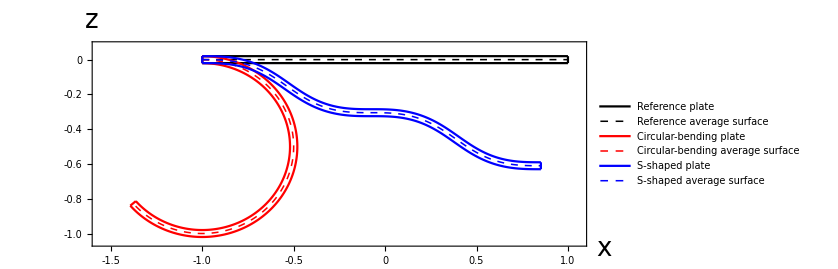

```mathematica
(* ---------------------------------------------------------------- *)
(* 11.1 Numerical current average surfaces and plate configurations *)
(* ---------------------------------------------------------------- *)

ParCompAsw = {L -> 1., h -> 1/50, λG -> 1., κG -> 2.};
ParAsw = {L -> 1., h -> 1/50, λG -> 1., κ0 -> 2.};

lAsw = L /. ParAsw;
hAsw = h /. ParAsw;

(* ---------------------------------------------------------------- *)
(* Compatible circular bending                                      *)
(* ---------------------------------------------------------------- *)

lCompAsw = L /. ParCompAsw;
hCompAsw = h /. ParCompAsw;
lambdaGCompAsw = λG /. ParCompAsw;
kappaGCompAsw = κG /. ParCompAsw;

xCompAsw[x_, z_] := -lCompAsw + (1/kappaGCompAsw + z) Sin[lambdaGCompAsw kappaGCompAsw (x + lCompAsw)];
zCompAsw[x_, z_] := -1/kappaGCompAsw + (1/kappaGCompAsw + z) Cos[lambdaGCompAsw kappaGCompAsw (x + lCompAsw)];

PosCompNumAsw[x_, z_] := {xCompAsw[x, z], zCompAsw[x, z]};
CenterCompAsw[x_] := PosCompNumAsw[x, 0];

(* ---------------------------------------------------------------- *)
(* Nonuniform growth: import A-SW exported data                     *)
(* ---------------------------------------------------------------- *)

folderASW50 = "C:\\Users\\June\\Desktop\\5_Example\\Data";

rawDefASW50 = Rest@Import[FileNameJoin[{folderASW50, "ASW_h50_3D_deformation_Oh2.csv"}], "CSV"];
rawCtrASW50 = Rest@Import[FileNameJoin[{folderASW50, "ASW_h50_xr_zr_Oh2.csv"}], "CSV"];

dataDefASW50Imp = N[rawDefASW50];
dataCtrASW50Imp = N[rawCtrASW50];

topCurveAsw = SortBy[Select[dataDefASW50Imp, Abs[#[[2]] - 1.] < 10^-10 &], First][[All, {3, 4}]];
botCurveAsw = SortBy[Select[dataDefASW50Imp, Abs[#[[2]] + 1.] < 10^-10 &], First][[All, {3, 4}]];
leftCurveAsw = SortBy[Select[dataDefASW50Imp, Abs[#[[1]] + 1.] < 10^-10 &], #[[2]] &][[All, {3, 4}]];
rightCurveAsw = SortBy[Select[dataDefASW50Imp, Abs[#[[1]] - 1.] < 10^-10 &], #[[2]] &][[All, {3, 4}]];
centerCurveAsw = SortBy[dataCtrASW50Imp, First][[All, {2, 3}]];

(* ---------------------------------------------------------------- *)
(* Reference configuration                                          *)
(* ---------------------------------------------------------------- *)

RefCenterAsw[x_] := {x, 0};
RefPosAsw[x_, z_] := {x, z};

(* ---------------------------------------------------------------- *)
(* Plot settings                                                    *)
(* ---------------------------------------------------------------- *)

xMinAsw = -1.55;
xMaxAsw = 1.05;
zMinAsw = -1.05;
zMaxAsw = 0.08;

fontSizeTickAsw = 18;
fontSizeLabelAsw = 26;

xTicksAsw = {{-1.5, "-1.5"}, {-1.0, "-1.0"}, {-0.5, "-0.5"}, {0, "0"}, {0.5, "0.5"}, {1.0, "1.0"}};
zTicksAsw = {{-1.0, "-1.0"}, {-0.8, "-0.8"}, {-0.6, "-0.6"}, {-0.4, "-0.4"}, {-0.2, "-0.2"}, {0, "0"}};

labZAsw = Style[TraditionalForm[z], FontFamily -> "Times", FontSize -> fontSizeLabelAsw, FontWeight -> Plain];
labXAsw = Style[TraditionalForm[x], FontFamily -> "Times", FontSize -> fontSizeLabelAsw, FontWeight -> Plain];

tickStyleAsw = Directive[FontFamily -> "Times", FontSize -> fontSizeTickAsw, Black];
frameStyleAsw = Directive[Black, AbsoluteThickness[2.0]];

styleRefPlateAsw = Directive[Black, AbsoluteThickness[1.6]];
styleRefCenterAsw = Directive[Black, Dashed, AbsoluteThickness[1.1]];
styleCompPlateAsw = Directive[Red, AbsoluteThickness[1.6]];
styleCompCenterAsw = Directive[Red, Dashed, AbsoluteThickness[1.1]];
styleDefPlateAsw = Directive[Blue, AbsoluteThickness[1.6]];
styleCurCenterAsw = Directive[Blue, Dashed, AbsoluteThickness[1.1]];

(* ---------------------------------------------------------------- *)
(* Reference plate                                                  *)
(* ---------------------------------------------------------------- *)

pSurfRefAsw = ParametricPlot[Evaluate[{RefPosAsw[x, hAsw], RefPosAsw[x, -hAsw]}], {x, -lAsw, lAsw}, PlotStyle -> styleRefPlateAsw, PlotPoints -> 150];
pSideRefAsw = ParametricPlot[Evaluate[{RefPosAsw[-lAsw, z], RefPosAsw[lAsw, z]}], {z, -hAsw, hAsw}, PlotStyle -> styleRefPlateAsw, PlotPoints -> 50];
pCenterRefAsw = ParametricPlot[Evaluate[RefCenterAsw[x]], {x, -lAsw, lAsw}, PlotStyle -> styleRefCenterAsw, PlotPoints -> 150];

(* ---------------------------------------------------------------- *)
(* Circular-bending plate                                           *)
(* ---------------------------------------------------------------- *)

pSurfCompAsw = ParametricPlot[Evaluate[{PosCompNumAsw[x, hCompAsw], PosCompNumAsw[x, -hCompAsw]}], {x, -lCompAsw, lCompAsw}, PlotStyle -> styleCompPlateAsw, PlotPoints -> 200];
pSideCompAsw = ParametricPlot[Evaluate[{PosCompNumAsw[-lCompAsw, z], PosCompNumAsw[lCompAsw, z]}], {z, -hCompAsw, hCompAsw}, PlotStyle -> styleCompPlateAsw, PlotPoints -> 50];
pCenterCompAsw = ParametricPlot[Evaluate[CenterCompAsw[x]], {x, -lCompAsw, lCompAsw}, PlotStyle -> styleCompCenterAsw, PlotPoints -> 200];

(* ---------------------------------------------------------------- *)
(* S-shaped plate imported from A-SW export                         *)
(* ---------------------------------------------------------------- *)

pSurfAsw = ListLinePlot[{topCurveAsw, botCurveAsw}, PlotStyle -> styleDefPlateAsw, AspectRatio -> Automatic];
pSideAsw = ListLinePlot[{leftCurveAsw, rightCurveAsw}, PlotStyle -> styleDefPlateAsw, AspectRatio -> Automatic];
pCenterAsw = ListLinePlot[centerCurveAsw, PlotStyle -> styleCurCenterAsw, AspectRatio -> Automatic];

(* ---------------------------------------------------------------- *)
(* Combined plot                                                    *)
(* ---------------------------------------------------------------- *)

pPlateAswCore = Show[pSurfRefAsw, pSideRefAsw, pCenterRefAsw, pSurfCompAsw, pSideCompAsw, pCenterCompAsw, pSurfAsw, pSideAsw, pCenterAsw, PlotRange -> {{xMinAsw, xMaxAsw}, {zMinAsw, zMaxAsw}}, Axes -> False, Frame -> True, FrameStyle -> frameStyleAsw, FrameTicks -> {{zTicksAsw, None}, {xTicksAsw, None}}, FrameTicksStyle -> tickStyleAsw, AspectRatio -> (zMaxAsw - zMinAsw)/(xMaxAsw - xMinAsw), ImageSize -> 620, PlotRangeClipping -> False, ImagePadding -> {{55, 30}, {42, 28}}, Epilog -> {Inset[labZAsw, Offset[{0, 8}, Scaled[{0, 1}]], {Center, Bottom}], Inset[labXAsw, Offset[{10, -3}, Scaled[{1, 0}]], {Left, Center}]}];

legendAsw = LineLegend[{styleRefPlateAsw, styleRefCenterAsw, styleCompPlateAsw, styleCompCenterAsw, styleDefPlateAsw, styleCurCenterAsw}, {"Reference plate", "Reference average surface", "Circular-bending plate", "Circular-bending average surface", "S-shaped plate", "S-shaped average surface"}, LegendLayout -> "Column", LegendMarkerSize -> 34, LabelStyle -> Directive[FontFamily -> "Times", FontSize -> 16]];

pPlateAsw = Legended[pPlateAswCore, Placed[legendAsw, Right]]
```

```mathematica
figureDir = FileNameJoin[{"C:", "Users", "June", "Desktop", "5_Example", "Figure"}];
If[! DirectoryQ[figureDir], CreateDirectory[figureDir]];

Export[FileNameJoin[{figureDir, "pPlateAsw.pdf"}], pPlateAsw];
```

A-SW points = 10593

B-SV points = 10593

Abaqus points = 16033

Common (x-X)/L range = {-0.151581,0.00355042}

Common (z-Z)/h range = {-30.5126,0.}

(x-X)/L color-bar ticks = {{-0.151581,-0.152},{-0.112798,-0.113},{-0.0740152,-0.074},{-0.0352324,-0.035},{0.00355042,0.004}}

(z-Z)/h color-bar ticks = {{-30.5126,-30.513},{-22.8844,-22.884},{-15.2563,-15.256},{-7.62814,-7.628},{0.,0}}

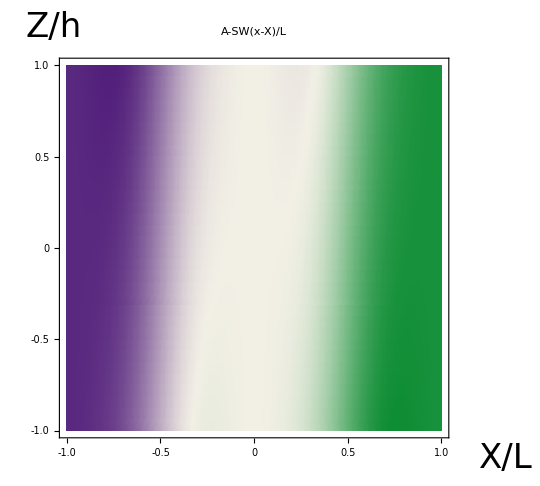
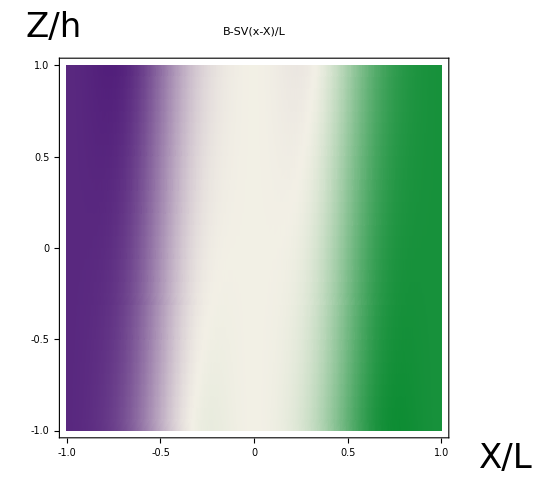
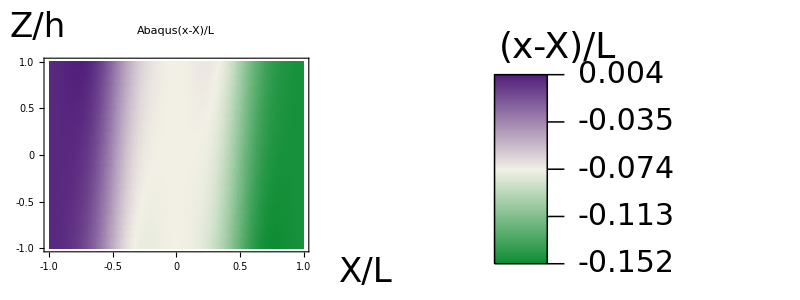
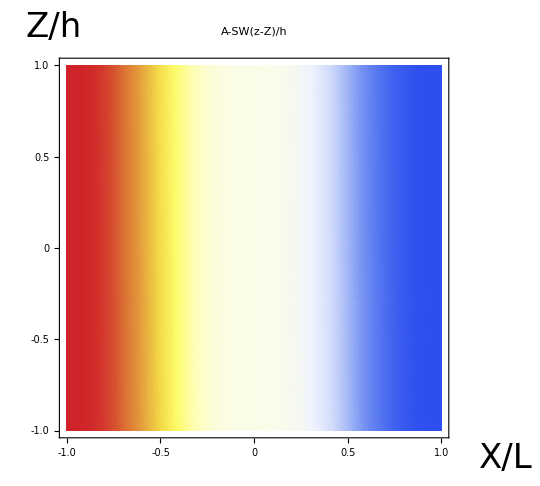
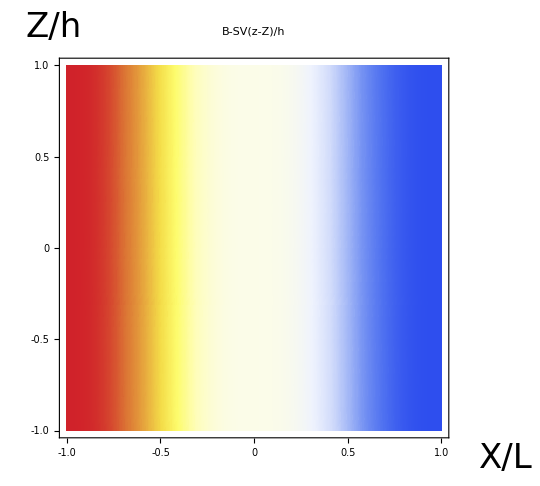
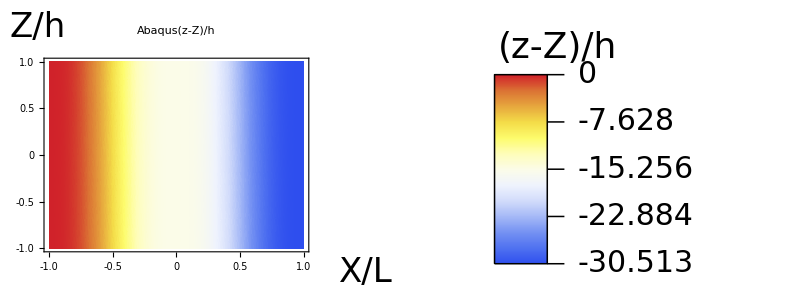
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

Saved: C:\Users\June\Desktop\5_Example\Figure\ASW_BSV_Abaqus_scaled_displacement_contours.pdf

File size = 6.71314 MB

C:\Users\June\Desktop\5_Example\Figure\ASW_BSV_Abaqus_scaled_displacement_contours.pdf

```mathematica
(* ---------------------------------------------------------------- *)
(* 11.2 Full-field scaled displacement contours                     *)
(*      A-SW, B-SV and Abaqus                                      *)
(* ---------------------------------------------------------------- *)

baseDir112 = "C:\\Users\\June\\Desktop\\5_Example";
dataDir112 = FileNameJoin[{baseDir112, "Data"}];
figureDir112 = FileNameJoin[{baseDir112, "Figure"}];
If[!DirectoryQ[figureDir112], CreateDirectory[figureDir112]];

fileAsw112 = FileNameJoin[{dataDir112, "ASW_h50_3D_deformation_Oh2.csv"}];
fileBsv112 = FileNameJoin[{dataDir112, "BSV_h50_3D_deformation_Oh2.csv"}];
fileAbaqus112 = FileNameJoin[{dataDir112, "U_position_h50_320_nonuniform_C3D20H.csv"}];

Lscale112 = 1.0;
hscale112 = 1.0/50.0;

(* ---------------------------------------------------------------- *)
(* 11.2.1 A-SW and B-SV data                                       *)
(* ---------------------------------------------------------------- *)

rawAsw112 = Import[fileAsw112, "CSV"];
rawBsv112 = Import[fileBsv112, "CSV"];

dataAsw112 = Select[ToExpression /@ Rest[rawAsw112], Length[#] >= 6 && VectorQ[Take[#, 6], NumericQ] &];
dataBsv112 = Select[ToExpression /@ Rest[rawBsv112], Length[#] >= 6 && VectorQ[Take[#, 6], NumericQ] &];

u1ScaledDataAsw112 = N[dataAsw112[[All, {1, 2, 5}]]];
u3ScaledDataAsw112 = N[dataAsw112[[All, {1, 2, 6}]]];
u1ScaledDataAsw112[[All, 3]] = u1ScaledDataAsw112[[All, 3]]/Lscale112;
u3ScaledDataAsw112[[All, 3]] = u3ScaledDataAsw112[[All, 3]]/hscale112;

u1ScaledDataBsv112 = N[dataBsv112[[All, {1, 2, 5}]]];
u3ScaledDataBsv112 = N[dataBsv112[[All, {1, 2, 6}]]];
u1ScaledDataBsv112[[All, 3]] = u1ScaledDataBsv112[[All, 3]]/Lscale112;
u3ScaledDataBsv112[[All, 3]] = u3ScaledDataBsv112[[All, 3]]/hscale112;

(* ---------------------------------------------------------------- *)
(* 11.2.2 Abaqus data                                               *)
(* ---------------------------------------------------------------- *)

rawAbaqus112 = Import[fileAbaqus112, "CSV"];
headerAbaqus112 = First[rawAbaqus112];
rowsAbaqus112 = Rest[rawAbaqus112];

colAbaqus112[name_] := First@FirstPosition[headerAbaqus112, name];

iXA112 = colAbaqus112["X"];
iZA112 = colAbaqus112["Z"];
iU1A112 = colAbaqus112["U1"];
iU3A112 = colAbaqus112["U3"];

toNum112[v_] := If[NumericQ[v], N[v], Quiet@Check[ToExpression[v], v]];

abaqusNumeric112 = ({toNum112[#[[iXA112]]], toNum112[#[[iZA112]]], toNum112[#[[iU1A112]]], toNum112[#[[iU3A112]]]} &) /@ rowsAbaqus112;
abaqusNumeric112 = Select[abaqusNumeric112, VectorQ[#, NumericQ] &];

u1ScaledDataAbaqusRaw112 = ({#[[1]]/Lscale112, #[[2]]/hscale112, #[[3]]/Lscale112} &) /@ abaqusNumeric112;
u3ScaledDataAbaqusRaw112 = ({#[[1]]/Lscale112, #[[2]]/hscale112, #[[4]]/hscale112} &) /@ abaqusNumeric112;

averageXZ112[data_] := ({#[[1, 1]], #[[1, 2]], Mean[#[[All, 3]]]} &) /@ GatherBy[data, Round[#[[1 ;; 2]], 10^-10] &];

u1ScaledDataAbaqus112 = N[averageXZ112[u1ScaledDataAbaqusRaw112]];
u3ScaledDataAbaqus112 = N[averageXZ112[u3ScaledDataAbaqusRaw112]];

Print["A-SW points = ", Length[u1ScaledDataAsw112]];
Print["B-SV points = ", Length[u1ScaledDataBsv112]];
Print["Abaqus points = ", Length[u1ScaledDataAbaqus112]];

(* ---------------------------------------------------------------- *)
(* 11.2.3 Common scaled displacement ranges                         *)
(* ---------------------------------------------------------------- *)

u1MinPlot112 = Min[Join[u1ScaledDataAsw112[[All, 3]], u1ScaledDataBsv112[[All, 3]], u1ScaledDataAbaqus112[[All, 3]]]];
u1MaxPlot112 = Max[Join[u1ScaledDataAsw112[[All, 3]], u1ScaledDataBsv112[[All, 3]], u1ScaledDataAbaqus112[[All, 3]]]];

u3MinPlot112 = Min[Join[u3ScaledDataAsw112[[All, 3]], u3ScaledDataBsv112[[All, 3]], u3ScaledDataAbaqus112[[All, 3]]]];
u3MaxPlot112 = 0.0;

Print["Common (x-X)/L range = ", {u1MinPlot112, u1MaxPlot112}];
Print["Common (z-Z)/h range = ", {u3MinPlot112, u3MaxPlot112}];

(* ---------------------------------------------------------------- *)
(* 11.2.4 Plot settings                                             *)
(* ---------------------------------------------------------------- *)

fontSizeTick112 = 32;
fontSizeLabel112 = 34;
fontSizeTitle112 = 36;
fontSizeLegend112 = 36;
fontSizeLegendTick112 = 30;

plotImageSize112 = 540;
legendImageSize112 = {230, 455};

xTicks112 = {{-1., "-1.0"}, {-0.5, "-0.5"}, {0., "0"}, {0.5, "0.5"}, {1., "1.0"}};
zTicks112 = {{-1., "-1.0"}, {-0.5, "-0.5"}, {0., "0"}, {0.5, "0.5"}, {1., "1.0"}};

frameStyle112 = Directive[Black, AbsoluteThickness[2.6]];
tickStyle112 = Directive[FontFamily -> "Times", FontSize -> fontSizeTick112, Black];

labX112 = Style["X/L", FontFamily -> "Times", FontSize -> fontSizeLabel112, FontSlant -> Italic];
labZ112 = Style["Z/h", FontFamily -> "Times", FontSize -> fontSizeLabel112, FontSlant -> Italic];

titleU1Asw112 = Row[{Style["A-SW", FontFamily -> "Times", FontSize -> fontSizeTitle112, FontWeight -> "Medium"], Spacer[12], Style["(x-X)/L", FontFamily -> "Times", FontSize -> fontSizeTitle112, FontSlant -> Italic]}];
titleU1Bsv112 = Row[{Style["B-SV", FontFamily -> "Times", FontSize -> fontSizeTitle112, FontWeight -> "Medium"], Spacer[12], Style["(x-X)/L", FontFamily -> "Times", FontSize -> fontSizeTitle112, FontSlant -> Italic]}];
titleU1Abaqus112 = Row[{Style["Abaqus", FontFamily -> "Times", FontSize -> fontSizeTitle112, FontWeight -> "Medium"], Spacer[12], Style["(x-X)/L", FontFamily -> "Times", FontSize -> fontSizeTitle112, FontSlant -> Italic]}];

titleU3Asw112 = Row[{Style["A-SW", FontFamily -> "Times", FontSize -> fontSizeTitle112, FontWeight -> "Medium"], Spacer[12], Style["(z-Z)/h", FontFamily -> "Times", FontSize -> fontSizeTitle112, FontSlant -> Italic]}];
titleU3Bsv112 = Row[{Style["B-SV", FontFamily -> "Times", FontSize -> fontSizeTitle112, FontWeight -> "Medium"], Spacer[12], Style["(z-Z)/h", FontFamily -> "Times", FontSize -> fontSizeTitle112, FontSlant -> Italic]}];
titleU3Abaqus112 = Row[{Style["Abaqus", FontFamily -> "Times", FontSize -> fontSizeTitle112, FontWeight -> "Medium"], Spacer[12], Style["(z-Z)/h", FontFamily -> "Times", FontSize -> fontSizeTitle112, FontSlant -> Italic]}];

labelU1112 = Style["(x-X)/L", FontFamily -> "Times", FontSize -> fontSizeLegend112, FontSlant -> Italic];
labelU3112 = Style["(z-Z)/h", FontFamily -> "Times", FontSize -> fontSizeLegend112, FontSlant -> Italic];

colorU1112 = Function[u, Blend[{RGBColor[0.05, 0.55, 0.20], RGBColor[0.95, 0.94, 0.90], RGBColor[0.32, 0.12, 0.48]}, Clip[Rescale[u, {u1MinPlot112, u1MaxPlot112}], {0, 1}]]];

colorU3112 = Function[u, ColorData["TemperatureMap"][Clip[Rescale[u, {u3MinPlot112, u3MaxPlot112}], {0, 1}]]];

(* ---------------------------------------------------------------- *)
(* 11.2.5 Five equally spaced color-bar ticks                       *)
(* ---------------------------------------------------------------- *)

fmt112[v_] := If[Abs[N[v]] < 5.*10^-4, "0", ToString[NumberForm[N[v], {7, 3}, NumberPadding -> {"", "0"}]]];

makeFiveTicks112[min_, max_] := Module[{vals}, vals = N[Subdivide[min, max, 4]]; ({#, fmt112[#]} &) /@ vals];

ticksU1112 = makeFiveTicks112[u1MinPlot112, u1MaxPlot112];
ticksU3112 = makeFiveTicks112[u3MinPlot112, u3MaxPlot112];

Print["(x-X)/L color-bar ticks = ", ticksU1112];
Print["(z-Z)/h color-bar ticks = ", ticksU3112];

(* ---------------------------------------------------------------- *)
(* 11.2.6 Manual elongated color bar                                *)
(* ---------------------------------------------------------------- *)

makeManualBar112[colorFunc_, {min_, max_}, ticks_, label_, imageSize_, tickFontSize_] := Module[{n = 400, barWidth = 0.20, barHeight = 1.28, tickLength = 0.065, strips, tickGraphics, y},
  strips = Table[{colorFunc[min + (i - 0.5)/n (max - min)], EdgeForm[None], Rectangle[{0., (i - 1.)/n barHeight}, {barWidth, i/n barHeight}]}, {i, 1, n}];
  tickGraphics = Table[y = Rescale[ticks[[i, 1]], {min, max}, {0., barHeight}]; {Black, AbsoluteThickness[1.1], Line[{{barWidth, y}, {barWidth + tickLength, y}}], Text[Style[ticks[[i, 2]], FontFamily -> "Times", FontSize -> tickFontSize, Black], {barWidth + tickLength + 0.05, y}, {-1, 0}]}, {i, 1, Length[ticks]}];
  Graphics[{strips, Black, AbsoluteThickness[1.1], Line[{{0., 0.}, {barWidth, 0.}, {barWidth, barHeight}, {0., barHeight}, {0., 0.}}], tickGraphics, Text[label, {0.24, barHeight + 0.18}, {0, 0}]}, PlotRange -> {{-0.22, 1.02}, {-0.06, barHeight + 0.32}}, PlotRangePadding -> None, ImageSize -> imageSize, AspectRatio -> Automatic, Background -> White]
];

legendU1112 = makeManualBar112[colorU1112, {u1MinPlot112, u1MaxPlot112}, ticksU1112, labelU1112, legendImageSize112, fontSizeLegendTick112];
legendU3112 = makeManualBar112[colorU3112, {u3MinPlot112, u3MaxPlot112}, ticksU3112, labelU3112, legendImageSize112, fontSizeLegendTick112];

(* ---------------------------------------------------------------- *)
(* 11.2.7 Common plot function                                      *)
(* ---------------------------------------------------------------- *)

makeDispPlot112[data_, range_, colorFunc_, title_] := ListDensityPlot[
  data,
  PlotRange -> {{-1., 1.}, {-1., 1.}, range},
  PlotRangePadding -> None,
  ColorFunction -> colorFunc,
  ColorFunctionScaling -> False,
  InterpolationOrder -> 1,
  Mesh -> False,
  Frame -> True,
  Axes -> False,
  FrameStyle -> frameStyle112,
  FrameTicks -> {{zTicks112, None}, {xTicks112, None}},
  FrameTicksStyle -> tickStyle112,
  AspectRatio -> 0.90,
  ImageSize -> plotImageSize112,
  PlotRangeClipping -> False,
  ImagePadding -> {{90, 110}, {70, 92}},
  BaseStyle -> {FontFamily -> "Times", FontSize -> 30, FontWeight -> "Medium"},
  Epilog -> {
    Inset[title, Offset[{0, 22}, Scaled[{0.5, 1}]], {Center, Bottom}],
    Inset[labZ112, Offset[{-6, 14}, Scaled[{0, 1}]], {Center, Bottom}],
    Inset[labX112, Offset[{30, -4}, Scaled[{1, 0}]], {Left, Top}]
  }
];

(* ---------------------------------------------------------------- *)
(* 11.2.8 (x-X)/L                                                   *)
(* ---------------------------------------------------------------- *)

pU1Asw112 = makeDispPlot112[u1ScaledDataAsw112, {u1MinPlot112, u1MaxPlot112}, colorU1112, titleU1Asw112];
pU1Bsv112 = makeDispPlot112[u1ScaledDataBsv112, {u1MinPlot112, u1MaxPlot112}, colorU1112, titleU1Bsv112];
pU1Abaqus112 = makeDispPlot112[u1ScaledDataAbaqus112, {u1MinPlot112, u1MaxPlot112}, colorU1112, titleU1Abaqus112];

figU1Abaqus112 = Grid[{{pU1Abaqus112, legendU1112}}, Spacings -> {0.10, 0}, Alignment -> Center];

(* ---------------------------------------------------------------- *)
(* 11.2.9 (z-Z)/h                                                   *)
(* ---------------------------------------------------------------- *)

pU3Asw112 = makeDispPlot112[u3ScaledDataAsw112, {u3MinPlot112, u3MaxPlot112}, colorU3112, titleU3Asw112];
pU3Bsv112 = makeDispPlot112[u3ScaledDataBsv112, {u3MinPlot112, u3MaxPlot112}, colorU3112, titleU3Bsv112];
pU3Abaqus112 = makeDispPlot112[u3ScaledDataAbaqus112, {u3MinPlot112, u3MaxPlot112}, colorU3112, titleU3Abaqus112];

figU3Abaqus112 = Grid[{{pU3Abaqus112, legendU3112}}, Spacings -> {0.10, 0}, Alignment -> Center];

(* ---------------------------------------------------------------- *)
(* 11.2.10 Six-panel figure                                        *)
(* ---------------------------------------------------------------- *)

figDisp112 = Grid[
  {{pU1Asw112, pU1Bsv112, figU1Abaqus112},
   {pU3Asw112, pU3Bsv112, figU3Abaqus112}},
  Spacings -> {0.18, 0.30},
  Alignment -> Center
];

figDisp112

(* ---------------------------------------------------------------- *)
(* 11.2.11 Export high-resolution compressed PDF                    *)
(* ---------------------------------------------------------------- *)

figureFileDisp112 = FileNameJoin[{figureDir112, "ASW_BSV_Abaqus_scaled_displacement_contours.pdf"}];

figDisp112Raster = Rasterize[
  figDisp112,
  "Image",
  RasterSize -> 15000,
  ImageResolution -> 1200
];

Export[figureFileDisp112, figDisp112Raster, "PDF"];

Print["Saved: ", figureFileDisp112];
Print["File size = ", N[FileByteCount[figureFileDisp112]/1024.^2], " MB"];

figureFileDisp112
```